```mathematica
frekvenceU=1200;
amplitudaU=5;
frekvenceI=2400;
amplitudaI=0.1;
soucastky={R1->10*10^3,R2->22*10^3,R3->33*10^3,C1->56*10^-9,C2->47*10^-9,L->82*10^-6};
vstup1={uZ[t]->amplitudaU*(Sin[2*Pi*frekvenceU*t])/2};
vstup2={iZ[t]->amplitudaI*(Sin[2*Pi*frekvenceI*t])/2};
```

```mathematica
uzel1=iU[t]==iR1[t];
uzel2=iR1[t]==iR2[t]+iC1[t]+iL[t];
uzel3=iL[t]==iR3[t]+iC2[t];
```

```mathematica
zdrojU=uZ[t]==u1[t];
zdrojI=iZ[t]==iR1[t]+iR2[t]+iC1[t]+iL[t];
rezR1=u1[t]-u2[t]==iR1[t]*R1;
rezR2=u2[t]==iR2[t]*R2;
rezR3=u3[t]==iR3[t]*R3;
kondC1=iC1[t]==u2'[t]*C1;
kondC2=iC2[t]==u3'[t]*C2;
civL=u2[t]-u3[t]==iL'[t]*L;
```

```mathematica
poc1=u2[0]==0;
poc2=u3[0]==0;
poc3=iL[0]==0;
```

```mathematica
rovnice={uzel1,uzel2,uzel3,zdrojU,zdrojI,rezR1,rezR2,rezR3,kondC1,kondC2,civL,poc1,poc2,poc3};
```

```mathematica
rovniceDosazena1=(rovnice/.soucastky)/.vstup1;
rovniceDosazena2=(rovnice/.soucastky)/.vstup2;
```

```mathematica
nezname={u1[t],u2[t],u3[t],iU[t],iR1[t],iR2[t],iR3[t],iC1[t],iC2[t],iL[t]};
```

```mathematica
perioda1=1/frekvenceU;
tmax1=5*perioda1;
```

```mathematica
perioda2=1/frekvenceI;
tmax2=5*perioda2;
```

```mathematica
reseni1=NDSolve[rovniceDosazena1,nezname,{t,0,tmax1},StartingStepSize->10^-9];
reseni2=NDSolve[rovniceDosazena2,nezname,{t,0,tmax2},StartingStepSize->10^-9];
```

NDSolve::overdet: There are fewer dependent variables, {iC1[t],iC2[t],iL[t],iR1[t],iR2[t],iR3[t],iU[t],u1[t],u2[t],u3[t]}, than equations, so the system is overdetermined.

```mathematica
Plot[{u1[t]/.reseni1,u2[t]/.reseni1,u3[t]/.reseni1},{t,0,tmax1}]
```

NDSolve::dsvar: 8.5119×10^-8 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{iU[8.5119×10^-8]==iR1[8.5119×10^-8],iR1[8.5119×10^-8]==iC1[8.5119×10^-8]+iL[8.5119×10^-8]+iR2[8.5119×10^-8],iL[8.5119×10^-8]==iC2[8.5119×10^-8]+iR3[8.5119×10^-8],0.00160446==u1[8.5119×10^-8],«3»,u3[8.5119×10^-8]==33000 iR3[8.5119×10^-8],iC1[8.5119×10^-8]==(7 u2'[8.5119×10^-8])/125000000,iC2[8.5119×10^-8]==(47 u3'[8.5119×10^-8])/1000000000,«4»},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 8.5119×10^-8 cannot be used as a variable.

ReplaceAll::reps: {«1»} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000851191 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

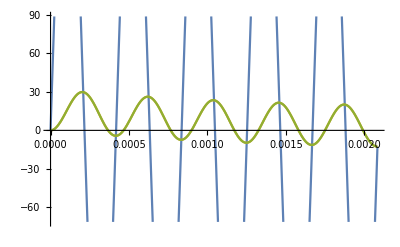

```mathematica
Plot[{u1[t]/.reseni2,u2[t]/.reseni2,u3[t]/.reseni2},{t,0,tmax2}]
```